```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
μ0 = 3.82828
```

3.82828

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]];
```

```mathematica
xs = Solve[im==0,x];
```

```mathematica
x0s =Select[Flatten[xs/.{μ-> μ0, y-> 0}],# ⟦2⟧<0.5&];
```

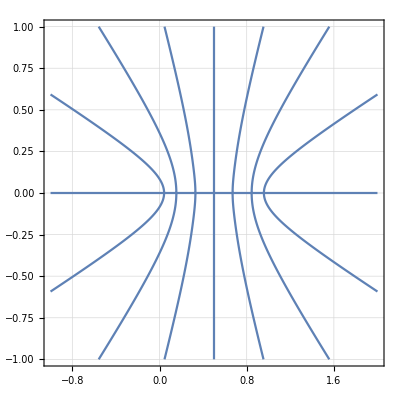

```mathematica
imμ =im/.μ-> μ0;
ContourPlot[imμ== 0,{x,-1,2},{y,-1,1},GridLines->Automatic, MaxRecursion->5]
```

```mathematica
rlist={};
Do[AppendTo[rlist, FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦i,1,2⟧/.{y-> ys⟦i,1,2⟧}/.x-> x0 ]/.μ-> μ0],{i,{2,3}}];
```

```mathematica
ϵlist = {};
Do[AppendTo[ϵlist, Reduce[Abs[rlist⟦i⟧]== 1,ϵ,Reals]],{i,{1,2}}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Abs[ϵmax].

Part::partw: Part 2 of {{{0.361396+0. ⅈ,0.00014951},{0.361257+0. ⅈ,0.000249734},{0.361119+0. ⅈ,0.000349959},{0.360981+0. ⅈ,0.000450183},«43»,{0.354865+0. ⅈ,0.0048605},{0.354725+0. ⅈ,0.00496074},{0.354586+0. ⅈ,0.00506099},«1495»}} does not exist.

Set::partw: Part 2 of {{{0.361396+0. ⅈ,0.00014951},{0.361257+0. ⅈ,0.000249734},{0.361119+0. ⅈ,0.000349959},{0.360981+0. ⅈ,0.000450183},«43»,{0.354865+0. ⅈ,0.0048605},{0.354725+0. ⅈ,0.00496074},{0.354586+0. ⅈ,0.00506099},«1495»}} does not exist.

Part::partw: Part 3 of {{{0.361396+0. ⅈ,0.00014951},{0.361257+0. ⅈ,0.000249734},{0.361119+0. ⅈ,0.000349959},{0.360981+0. ⅈ,0.000450183},«43»,{0.354865+0. ⅈ,0.0048605},{0.354725+0. ⅈ,0.00496074},{0.354586+0. ⅈ,0.00506099},«1495»}} does not exist.

Set::partw: Part 3 of {{{0.361396+0. ⅈ,0.00014951},{0.361257+0. ⅈ,0.000249734},{0.361119+0. ⅈ,0.000349959},{0.360981+0. ⅈ,0.000450183},«43»,{0.354865+0. ⅈ,0.0048605},{0.354725+0. ⅈ,0.00496074},{0.354586+0. ⅈ,0.00506099},«1495»}} does not exist.

Part::partw: Part 2 of {{{0.361396+0. ⅈ,-0.00014951},{0.361257+0. ⅈ,-0.0000497341},{0.361119+0. ⅈ,0.0000500415},{0.360981+0. ⅈ,0.000149817},«43»,{0.354865+0. ⅈ,0.0045395},{0.354725+0. ⅈ,0.00463926},{0.354586+0. ⅈ,0.00473901},«1495»}} does not exist.

Set::partw: Part 2 of {{{0.361396+0. ⅈ,-0.00014951},{0.361257+0. ⅈ,-0.0000497341},{0.361119+0. ⅈ,0.0000500415},{0.360981+0. ⅈ,0.000149817},«43»,{0.354865+0. ⅈ,0.0045395},{0.354725+0. ⅈ,0.00463926},{0.354586+0. ⅈ,0.00473901},«1495»}} does not exist.

Part::partw: Part 3 of {{{0.361396+0. ⅈ,-0.00014951},{0.361257+0. ⅈ,-0.0000497341},{0.361119+0. ⅈ,0.0000500415},{0.360981+0. ⅈ,0.000149817},«43»,{0.354865+0. ⅈ,0.0045395},{0.354725+0. ⅈ,0.00463926},{0.354586+0. ⅈ,0.00473901},«1495»}} does not exist.

Set::partw: Part 3 of {{{0.361396+0. ⅈ,-0.00014951},{0.361257+0. ⅈ,-0.0000497341},{0.361119+0. ⅈ,0.0000500415},{0.360981+0. ⅈ,0.000149817},«43»,{0.354865+0. ⅈ,0.0045395},{0.354725+0. ⅈ,0.00463926},{0.354586+0. ⅈ,0.00473901},«1495»}} does not exist.

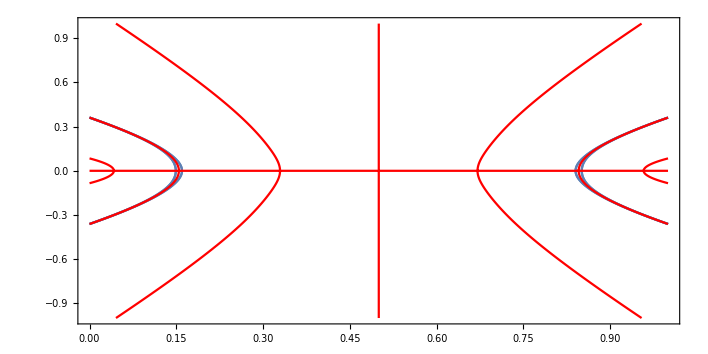

```mathematica
dp = 0;
up  = 1;
pplots={};
pplotsmin={};
pplotsmax={};

Do[
localpplotsmin={};
localpplotsmax={};
i=n-1;
f=StringLength[ToString[#]]&;
nonesquad = {};
group = SortBy[Chop[ϵlist⟦i⟧,10^-5],f];
strlen = Table[StringLength[ToString[group⟦k⟧]],{k,1,Length[ϵlist⟦i⟧]}];
Do[If[strlen⟦m⟧<100,AppendTo[nonesquad,m],None], {m,1,Length[ϵlist⟦i⟧]}];
ig = Range[Length[group]];
ig = Drop[ig,Length[nonesquad]];

Do[
ysn = ys⟦n,1,2⟧/.{μ-> μ0,x-> x0};
Which[
j== ig⟦1⟧,d=1.00001group⟦j,1,2⟧; u=1,
j== ig⟦2⟧, d=0;u=0.9999group⟦j,1,2⟧,
j> ig⟦2⟧, d= 1.00001group⟦j,1,1⟧;u=0.999999group⟦j,1,5⟧];
part1 = group⟦j,2,1,2⟧;
part2 = group⟦j,2,2,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part1, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part1, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0+part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];

AppendTo[localpplotsmin,Table[{ysn, x0+part1},{x0,d,u,0.0001}]];
localpplotsmin2= Select[Flatten[localpplotsmin,1],#⟦2⟧ <0.5&];
localpplotsmin3= Select[localpplotsmin2,Im[#⟦1⟧]== 0& ];
localpplotsmin4= Select[localpplotsmin3,#⟦1⟧> 0& ];

AppendTo[localpplotsmax,Table[{ysn, x0-part1},{x0,d,u,0.0001}]];
localpplotsmax2 =Select[Flatten[localpplotsmax,1],#⟦2⟧ <0.5&];
localpplotsmax3= Select[localpplotsmax2,Im[#⟦1⟧]== 0& ];
localpplotsmax4= Select[localpplotsmax3,#⟦1⟧> 0& ],

{j,ig}];
AppendTo[pplotsmax,localpplotsmax4];
AppendTo[pplotsmin,localpplotsmin4],

{n,{2,3}}];

ϵmax = Sort[DeleteDuplicates[Abs[ϵmax]]];
pplotsmax = Partition[pplotsmax,2];
Do[pplotsmax⟦i⟧ = Flatten[pplotsmax⟦i⟧,1],{i,{1,2,3}}]
pplotsmin = Partition[pplotsmin,2];
Do[pplotsmin⟦i⟧ = Flatten[pplotsmin⟦i⟧,1],{i,{1,2,3}}]

img = Show[pplots, ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic,ContourStyle->Red, MaxRecursion->5],PlotRange-> Automatic, AspectRatio-> 1/2]
```

```mathematica
f1max = Interpolation[pplotsmax⟦1⟧, InterpolationOrder->2, Method->"Hermite"];
f1min = Interpolation[pplotsmin⟦1⟧, InterpolationOrder->2, Method->"Hermite"];
```

```mathematica
upper = 0.2;
```

```mathematica
band1pts = {};
For[i=0,i<30000,i++;
py= RandomReal[{0,upper}];
pmax = Re[f1max[py]];
pmin = Re[f1min[py]];
px = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band1pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.187562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.12609} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

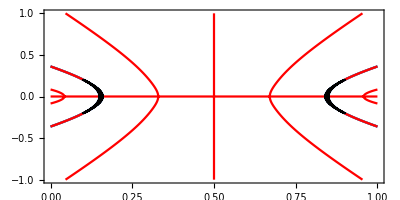

```mathematica
Show[img,ListPlot[band1pts, PlotStyle->Black]]
```

```mathematica
μ=μ0;
  stats3b1={};
For[i=0,i< Length[band1pts],i++;
x = band1pts⟦i,1⟧;
y = band1pts⟦i,2⟧;
For[j=0,j<3,j++;
{x1,y1} = {Re[map[x,y,μ]],Im[map[x,y,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[stats3b1,{x3,y3}]]]
```

```mathematica
Export["mu28.txt", stats3b1,"Table" ]1
```

mu28.txt